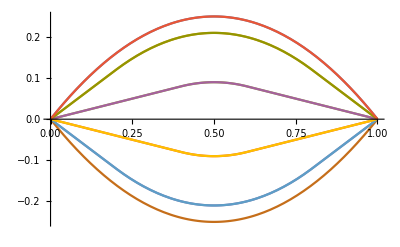

```mathematica
F[t_,x_]:=Sum[4*(m*π)^(-3)*(1-(-1)^m)*Cos[m*π*t]*Sin[m*π*x],{m,1,1000}]

Plot[{F[0,x],F[0.2,x],F[0.4,x],F[0.6,x],F[0.8,x],F[1,x],F[1.2,x],F[1.4,x],F[1.6,x],F[1.8,x],F[2,x]},{x,0,1}]
```